```mathematica
(*変数の初期化*)
ClearAll["Global`*"]
```

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

```mathematica
(*修正ブレットシュナイダー・光易型*)
S[H_,T_,f_]:=0.205*(H^2)*(T^-4)*(f^-5)*Exp[-0.75*(T*f)^-4];
```

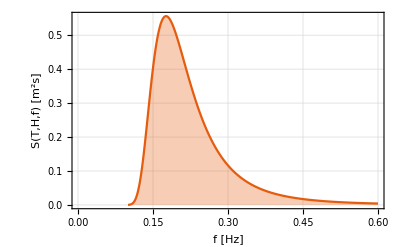

-Graphics3D-

```mathematica
(*有義波高と有義周期*)
H=1.;
T=5;
F=1/T;

(*プロット，またはサンプリングする範囲*)
minF=F/2;
maxF=3*F;

(*範囲を上のように調整すれば，スペクトル全体を常に表示できる*)
ListPlot[Table[{f,S[H,T,f]},{f,minF,maxF,0.001}]
,FrameLabel->{"f [Hz]","S(T,H,f) [m^2s]"}
,Evaluate[plot2Doption]
,GridLines->Automatic
,Filling->Bottom
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]

ListLinePlot3D[Table[{f,T,S[H,T,f]},{T,4,8,0.5},{f,0.5/T,3/T,0.01}]
,PlotRange->All
,Filling->Bottom
,Evaluate[plot3Doption]
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]
```

## スペクトルから有義波を計算する

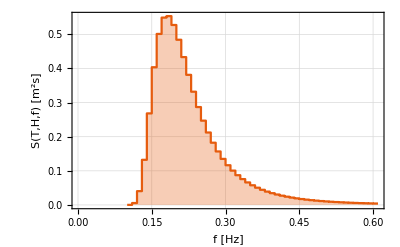

```mathematica
h=100;
g=9.81;

(*分散関係式*)
DispersionRelation[w_]:=k/.FindRoot[w^2==g*k*Tanh[k*h],{k,w^2/g}];

n=50;(*分割数*)
df=(maxF-minF)/n;(*スペクトルの分割刻み*)

ListStepPlot[Table[{minF+df*i,S[H,T,minF+df*i]},{i,0,n}]
,FrameLabel->{"f [Hz]","S(T,H,f) [m^2s]"}
,Evaluate[plot2Doption]
,GridLines->Automatic
,Filling->Bottom
(*,PlotLabel->StringJoin["修正ブレットシュナイダー・光易型スペクトル, ","H=",ToString[H],", T=",ToString[T]]*)
]
wave[x_,t_]=Quiet@Sum[Module[{f,w,k,a,theta},
f=minF+df*i;
w=2*π*f;
k=DispersionRelation[w];
a=Sqrt[2*S[H,T,f]*df];(*波の成分の振幅は，Sを使ってこれで求まるはず m^2*s=S[H,T,f]*)
theta=RandomReal[{0,2 π}];(*波の各成分の位相のずれはランダム*)
a*Cos[k*x-w*t+theta]],{i,0,n}];
```

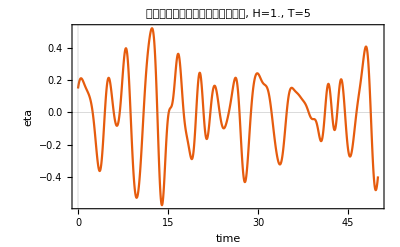

```mathematica
x=0.;
ListPlot[Table[{t,wave[x,t]},{t,0,10.*T,0.01*T}]
,Evaluate[plot2Doption]
,PlotTheme->"Scientific"
,PlotLabel->StringJoin["スペクトルから計算した不規則波, ","H=",ToString[H],", T=",ToString[T]]
,FrameLabel->{"time","eta"}
]
```

## 出力波形から有義波高と有義周期をゼロアップクロス法を使って計算

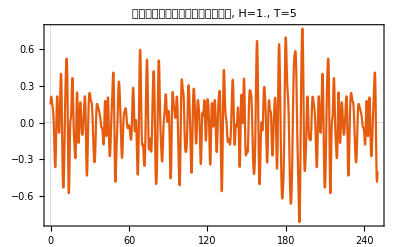

```mathematica
(*Generate wave data*)
data=Table[{t,wave[x,t]},{t,0,50.*T,0.01*T}];

ListPlot[data
,Evaluate[plot2Doption]
,PlotLabel->StringJoin["スペクトルから計算した不規則波, ","H=",ToString[H],", T=",ToString[T]]]
```

{90,140,219,303,394,442,503,577,696,824,865,929,1024,1115,1245,1302,1352,1455,1555,1638,1731,1855,1993,2094,2174,2240,2317,2387,2459,2495,2558,2637,2763,2854,2908,2940,3029,3136,3225,3249,3329,3414,3477,3577,3706,3828,3916,3991,4090,4140,4219,4303,4394,4442,4503,4577,4696,4824,4865,4929}

{49,120,176,265,353,419,473,539,646,769,847,890,976,1073,1169,1283,1311,1392,1494,1596,1680,1816,1948,2047,2134,2215,2280,2366,2425,2484,2526,2601,2693,2805,2877,2936,2974,3085,3179,3228,3295,3377,3449,3518,3645,3771,3874,3945,4049,4120,4176,4265,4353,4419,4473,4539,4646,4769,4847,4890,4976}

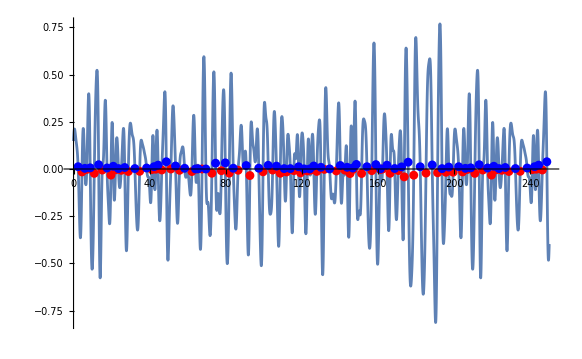

```mathematica
(*ゼロアップクロス点．これを使う*)
zeroUpCrossings=DeleteCases[Table[If[data[[i,2]]*data[[i+1,2]]<0&&data[[i,2]]<0&&data[[i+1,2]]>0,i],{i,1,Length[data]-1}],Null]
(*ゼロダウンクロス点*)
zeroDownCrossings=DeleteCases[Table[If[data[[i,2]]*data[[i+1,2]]<0&&data[[i,2]]>0&&data[[i+1,2]]<0,i],{i,1,Length[data]-1}],Null]

Show[
ListPlot[data,Joined->True],
ListPlot[Table[data[[i]],{i,zeroUpCrossings}],PlotStyle->Red],
ListPlot[Table[data[[i]],{i,zeroDownCrossings}],PlotStyle->Blue]]
```

```mathematica
(*Compute wave heights and periods*)waveHeights=Table[(*Find the peak after the current zero up-crossing and the trough before the next one*)dataSubset=data[[zeroUpCrossings[[i]];;zeroUpCrossings[[i+1]]]];
peak=Max[dataSubset[[All,2]]];
trough=Min[dataSubset[[All,2]]];
(*Compute the wave height as the difference between the peak and the trough*)
peak-trough,{i,1,Length[zeroUpCrossings]-1}]

wavePeriods=(data[[zeroUpCrossings[[#+1]],1]]-data[[zeroUpCrossings[[#]],1]])&/@Range[1,Length[zeroUpCrossings]-1]

(*Compute significant wave height and period*)
significantWaveHeight=Mean[Sort[waveHeights,Greater][[1;;Round[Length[waveHeights]/3]]]];
significantWavePeriod=Mean[Sort[wavePeriods,Greater][[1;;Round[Length[wavePeriods]/3]]]];

Print["有義波高 ",significantWaveHeight]
Print["有義周期 ",significantWavePeriod]
```

{0.29844,0.930001,1.10029,0.655,0.412366,0.265201,0.64896,0.566842,0.331582,0.287382,0.480663,0.892774,0.623254,0.256896,0.356243,0.446729,0.948341,0.752218,0.921907,0.827049,0.687792,0.762843,0.593794,0.715173,0.448769,0.522697,0.329774,0.534676,0.192101,0.424878,0.820946,0.611581,0.532707,0.485737,0.252552,0.628548,0.685954,1.17252,0.066712,0.619572,0.452626,0.578573,1.26164,1.36046,1.39756,1.16427,0.358764,0.576857,0.29844,0.930001,1.10029,0.655,0.412366,0.265201,0.64896,0.566842,0.331582,0.287382,0.480663}

{2.5,3.95,4.2,4.55,2.4,3.05,3.7,5.95,6.4,2.05,3.2,4.75,4.55,6.5,2.85,2.5,5.15,5.,4.15,4.65,6.2,6.9,5.05,4.,3.3,3.85,3.5,3.6,1.8,3.15,3.95,6.3,4.55,2.7,1.6,4.45,5.35,4.45,1.2,4.,4.25,3.15,5.,6.45,6.1,4.4,3.75,4.95,2.5,3.95,4.2,4.55,2.4,3.05,3.7,5.95,6.4,2.05,3.2}

有義波高 0.954352

有義周期 5.6075